# MWE : Creating a closed curve based on given points

## Creating the boundary shape

Here are some points that will form the basis for a closed curve and the polygon passing through those points:

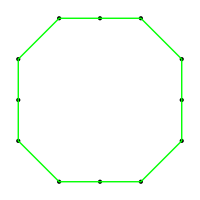

```mathematica
points={{2,-1},{2,0},{2,1},{1,2},{0,2},{-1,2},{-2,1},{-2,0},{-2,-1},{-1,-2},{0,-2},{1,-2}};
Graphics[{PointSize[Large],Point/@points,Green,Line[Append[points,points[[1]]]]},ImageSize->200]
```

Here is a smooth curve that approximates those points

```mathematica
curve=Graphics[{BSplineCurve[points,SplineClosed->True]},ImageSize->200]
```

-Graphics-

The Documentation Center entry for BSplineCurve has an example explaining how to ensure that your spline passes through the given points.

## Creating the filled-in shape

Use the FilledCurve function to create the filled-in shape

```mathematica
filled=Graphics[FilledCurve[{BSplineCurve[points,SplineClosed->True]}]]
```

-Graphics-

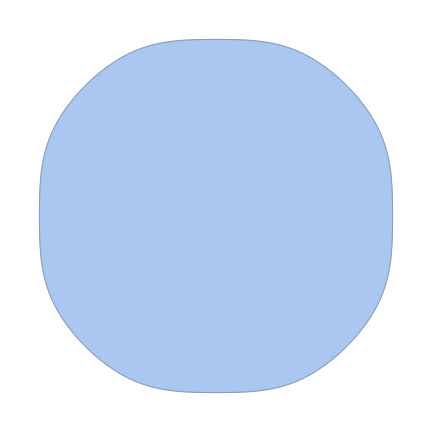

```mathematica
shape=BoundaryDiscretizeGraphics[filled,MaxCellMeasure->0.001];
Show[shape,ImageSize->200]
```